Basic Ternary Phase Diagram

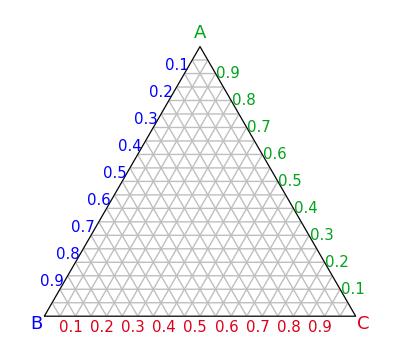

```mathematica
base=Graphics[{
{Thin,GrayLevel@0.75,
Line[{{#/2,#*√3/2},{1-#/2,#*√3/2}}],Line[{{#,0},{#/2,#*√3/2}}],Line[{{1-#,0},{1-#/2,#*√3/2}}]}&/@Range[0,1,0.05],
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,0},{0.5,√3/2},{1,0}}]},
{Text[Style[#,15,RGBColor[0.,0.64,0.1]],{1.04-#/2,#*√3/2}],Rotate[Text[Style[1-#,15,Blue],{#/2-0.025,#*√3/2+0.025}],-55 Degree],Rotate[Text[Style[#,15,RGBColor[0.86,0.,0.11]],{#-0.015,-0.035}],55 Degree]
}&/@Range[0.1,0.9,0.1],
Text[Style["A",18,RGBColor[0.,0.64,0.1]],{0.5,0.91}],
Text[Style["B",18,Blue],{-0.025,-0.025}],
Text[Style["C",18,RGBColor[0.86,0.,0.11]],{1.025,-0.025}]
}]
```

```mathematica
Manipulate[
Module[{px,py,length},
px=pt[[1]];py=pt[[2]];

If[px≤0.5∧py≥px*√3,pt={py/√3,py}];
If[px>0.5∧py≥(1-px)*√3,pt={1-py/√3,py}];

length[x_,y_]:=√((px-x)^2+(py-y)^2);

Show[base,
If[bac==1,
Graphics[{Thick,
RGBColor[0.,0.64,0.1],Arrow[{pt,{1-py/√3,py}}],
RGBColor[0.86,0.,0.11],Arrow[{pt,{px-py/√3,0}}],
Blue,Arrow[{pt,{0.5*(px+py/√3),0.5*(px+py/√3)*√3}}]
}],
Graphics[{
{Thick,
RGBColor[0.,0.64,0.1],Arrow[{pt,{px,0}}],
Blue,Arrow[{pt,{1-py/(√3)-1/4*(1-py/(√3)-px),py+(√3)/4*(1-py/(√3)-px)}}],
RGBColor[0.86,0.,0.11],Arrow[{pt,{py/(√3)+1/4*(px-py/(√3)),py+(√3)/4*(px-py/(√3))}}]},

(*A*)If[length[px,0]>0.16,Text[Framed[Style[NumberForm[py*2/√3,{2,2}],17,RGBColor[0.,0.64,0.1]],FrameStyle->None,FrameMargins->Tiny,Background->White],{px,0.5*py}]
],
(*B*)If[length[py/(√3)+1/4*(px-py/(√3)),py+(√3)/4*(px-py/(√3))]>0.2,Text[Framed[Style[NumberForm[px-py/√3,{2,2}],17,RGBColor[0.86,0.,0.11]],FrameStyle->None,FrameMargins->Tiny,Background->White],{0.5*(px+py/(√3)+1/4*(px-py/(√3))),0.5*(py+py+(√3)/4*(px-py/(√3)))}]
],
(*C*)If[length[1-py/(√3)-1/4*(1-py/(√3)-px),py+(√3)/4*(1-py/(√3)-px)]>0.2,Text[Framed[Style[NumberForm[1-(px+py/√3),{2,2}],17,Blue],FrameStyle->None,FrameMargins->Tiny,Background->White],{0.5*(px+1-py/(√3)-1/4*(1-py/(√3)-px)),0.5*(py+py+(√3)/4*(1-py/(√3)-px))}]
]
}]
],
Graphics[Text[Style[Column[{"mass fractions",
Framed@Column[{
Style[Row[{"component A = ",NumberForm[py*2/√3,{2,2}]}],RGBColor[0.,0.64,0.1]],
Style[Row[{"component B = ",NumberForm[1-(px+py/√3),{2,2}]}],Blue],
Style[Row[{"component C = ",NumberForm[px-py/√3,{2,2}]}],RGBColor[0.86,0.,0.11]]}]
},Center],17],{0.07,0.8}]],
ImageSize->{500,450}]
],Row[{
Control[{{bac,2,""},{1->" standard view ",2->" alternate view "},Setter}],
Control[{{pt,{0.55,0.3}},Locator,Appearance->Graphics[{Disk[]},ImageSize->13]}]
}],SaveDefinitions->True]
```

This Demonstration shows two alternative representations of a ternary phase diagram, which is used to describe the phase behavior of three-component mixtures. The black point, which can be moved by the user, represents the composition of the mixture, and each corner of the triangle is a pure component. The mass fraction of a component in the mixture is read off the axis that is the same color as that component in the standard view. A line is drawn through the point parallel to the base of the triangle that is opposite the corner corresponding to that pure component. In the alternate representation, the mass fraction of a component is determined by drawing a line through the point and perpendicular to the base opposite that component. The fraction of the distance from the base to the corner is the mass fraction of that component. These diagrams can also be drawn using mole fractions instead of mass fractions.

For a walk-through of this Demonstration, view the Screencast Ternary Phase Diagram Basics (Interactive Simulation)

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

ternary phase diagram

ternary diagram

thermodynamics

chemical engineering

separations

Ternary Phase Diagram with Phase Envelope

Ternary Phase Diagram with Alternate Phase Envelope

Contributed by: Megan E. Maguire

Additional contributions by: Rachael L. Baumann

(University of Colorado Boulder, Department of Chemical and Biological Engineering)